Day 3 Boat Calculations

```mathematica
Manipulate[Plot[2*Abs[x/2]^n, {x,-2,2},PlotRange->{{-2,2},{0,2}}, PlotTheme->"Scientific"],{n,1,6,Appearance->"Labeled"}]
```

```mathematica
n=2
```

2

```mathematica
N[Integrate[Integrate[500, {y, 2*Abs[x/2]^n, 2} ],{x, -2, 2}]]
```

2666.67

```mathematica
N[(1/%)*Integrate[Integrate[500*y, {y, 2*Abs[x/2]^n, 2} ],{x, -2, 2}]]
```

1.2

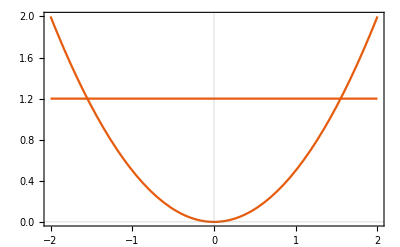

```mathematica
Show[Plot[2*Abs[x/2]^n, {x,-2,2},PlotRange->{{-2,2},{0,2}}, PlotTheme->"Scientific"],Plot[%, {x,-2,2},PlotRange->{{-2,2},{0,2}}, PlotTheme->"Scientific"] ]
```